# Force Inference: M1

### miscellaneous functions

```mathematica
ClearAll[segmentImage];
segmentImage[binarizedMask_?ImageQ,border: True|False]:=
Which[!border,
Print["border not present, segmenting with morphological components"];
ArrayComponents@DeleteBorderComponents@MorphologicalComponents[ColorNegate@binarizedMask, CornerNeighbors->False],
border,
Print["border exists, segmenting with watershed components"];
WatershedComponents[binarizedMask, CornerNeighbors->False]
];
```

```mathematica
Clear@bresenhamLine;
bresenhamLine[p0_,p1_]:=Module[{dx,dy,sx,sy,err,newp},
{dx,dy}=Abs[p1-p0];
{sx,sy}=Sign[p1-p0];
err=dx-dy;
newp[{x_,y_}]:=With[{e2=2 err},{If[e2>-dy,err-=dy;x+sx,x],If[e2<dx,err+=dx;y+sy,y]}];
NestWhileList[newp,p0,#=!=p1&,1]
];
```

```mathematica
Clear@closeImage;
closeImage[image_]:=Module[{morphImage, morphImagePos,posConv,ptsOrdered},
morphImage=MorphologicalTransform[image,"SkeletonEndPoints"];
morphImagePos=PixelValuePositions[morphImage,1];
posConv=With[{mean=Mean@N@morphImagePos},
ptsOrdered=Append[#,First@#]&[SortBy[morphImagePos,ArcTan@@(mean-#)&]];
DeleteDuplicates@Flatten[bresenhamLine@@@Partition[ptsOrdered,2,1,1],1]
];
ReplacePixelValue[image,posConv-> 1]
];
```

```mathematica
(*Comments: dist being passed to nearest function*)
ClearAll[associateVertices];
associateVertices[img_,segt_]:=Module[{pts,members,cellsTovertices,dim=Reverse@ImageDimensions@img},
pts=ImageValuePositions[MorphologicalTransform[img,{"Fill","SkeletonBranchPoints"}],1]; (* finding branch points *)
members=ParallelMap[Block[{elems},
elems=Dilation[ReplaceImageValue[ConstantImage[0,Reverse@dim],#->1],1];DeleteCases[Union@Flatten@ImageData[elems*Image[segt]],0|0.]]&,pts];
(* finding vertices with 2 or more neighbouring cells *)
cellsTovertices=MapAt[List,Cases[Thread[Round@members->pts],HoldPattern[pattern:{__}/;Length@pattern≥2->_]],{All,2}]
];
```

```mathematica
bintype[int_Integer?EvenQ]:=Floor[int/2];
bintype[int_Integer?OddQ]:=Floor[int/2]+1;

ClearAll@edgeMergerFn;
edgeMergerFn[edgelen_,edges_,cellToVertex_]:=Block[{edgesC=edges,cellToVertexC=cellToVertex,smalledgekeys,smalledges,verts,bins,alt,reprules},
smalledgekeys=Cases[edgelen,HoldPattern[key_->1]:>key];
If[smalledgekeys≠{},
reprules=If[Length[smalledgekeys]==1,
With[{mean=Mean@#},
#-> mean&/@#]&@Extract[edges,smalledgekeys],
smalledges=Extract[edges,Partition[smalledgekeys,1]];
verts=Flatten[smalledges,1];
bins=DeleteDuplicates@Map[bintype,DeleteDuplicates[Position[verts,#]&/@verts],{3}];
alt=Flatten@Cases[bins,{Repeated[{_},{2,∞}]}];
With[{mean=Mean[#]},
#->mean&/@#
]&@Cases[#,{__Real},{-2}]&@Extract[smalledges,#]&/@Replace[Replace[bins,{{Alternatives@@alt}}->Nothing,{1}],{{x_}}:> {x},{1}]
//DeleteDuplicates@*Flatten
];
If[reprules=={},Echo["edges do not need merging"],Echo["edges are merged"]];
{DeleteCases[edgesC/.reprules,{x_,x_}],Normal@AssociationMap[Reverse,GroupBy[cellToVertexC/.reprules,Last->First,Union@*Flatten]]},
Echo["No edge of pixel size 1 detected"];
{edgesC,cellToVertexC}
]
]
```

### inference functions

```mathematica
Clear@formAndComputeMatrices;
formAndComputeMatrices[vertexCoordinatelookup_,inds_,colsOrder_,edgenum_,delV_,vertexToCells_,vertexvertexConn_,maxcellLabels_,filteredvertices_,vertexAssoc_]:=Module[{tx,ty,tensinds,filteredvertexnum,relabelvert,spArrayTx,spArrayTy,spArrayPx,spArrayPy,spArrayX,spArrayY,$filteredvertices},

{tx,ty}=Transpose[
With[{target=vertexCoordinatelookup[#[[2]]],source=vertexCoordinatelookup[#[[1]]]},
(target-source)/Norm[target-source]
]&/@inds];

Print[Style["Tension coefficients computed: ",16],Style["☑",30]];MapThread[Print[Style["counts of zero coefficients "<>#1,Darker@Green,15],Style[ Count[#2,0.],15]]&,{{"Tx: ","Ty: "},{tx,ty}}];

$filteredvertices=Complement[filteredvertices,delV];filteredvertexnum=Length@$filteredvertices;relabelvert=AssociationThread[$filteredvertices-> Range[Length@$filteredvertices]];tensinds=Thread[{Lookup[relabelvert,Part[inds,All,1]],colsOrder}];spArrayTx=spArrayTy=SparseArray@ConstantArray[0,{filteredvertexnum,edgenum}];MapThread[(spArrayTx[[Sequence@@#1]]=#2)&,{tensinds,tx}];MapThread[(spArrayTy[[Sequence@@#1]]=#2)&,{tensinds,ty}];
MapThread[Print[Style[#1<> "coefficients stats: ",Blue,15],Style[Counts@Map[Total@*Unitize,Normal[#2]],15]]&,{{"Tx ", "Ty "},{spArrayTx,spArrayTy}}];
Print[Style["Tension coefficients distribution: ",15],Histogram[{{},Join[spArrayTx["NonzeroValues"],spArrayTy["NonzeroValues"]]},20,ImageSize->Small]];

spArrayPx=spArrayPy=SparseArray@ConstantArray[0,{filteredvertexnum,maxcellLabels}];

Block[{neighbouringCells,bisectionlabels,bisectpts,centroid,orderingT,vertexcoords,orderptsT,orderIndT,orderCells,kk=0,px,py},
With[{cellToVertexLabelsT= Reverse[vertexToCells,2],edgeVertexPart=GroupBy[vertexvertexConn~Flatten~1 ,First->Last]},
With[{cellToAllVerticesT= GroupBy[Flatten[Thread/@cellToVertexLabelsT],First-> Last]},
Do[
neighbouringCells= vertexToCells[[i,2]]; (* for vertex, the neighbouring cell labels *)
bisectionlabels=Intersection[cellToAllVerticesT[#],edgeVertexPart[i]]&/@neighbouringCells ;If[Length[neighbouringCells]>2 && MatchQ[bisectionlabels,{Repeated[{_,_},{3,∞}]}],
(vertexcoords=DeleteDuplicates[vertexCoordinatelookup[#]&/@Flatten@bisectionlabels];centroid=Mean@vertexcoords;orderingT=Ordering[ArcTan[Last@#-Last@centroid,First@#-First@centroid]&/@vertexcoords];orderptsT=vertexcoords[[orderingT]];orderIndT=Partition[Lookup[vertexAssoc,Append[orderptsT,First@orderptsT]],2,1];
orderCells =Last@@@Position[(x↦ Map[Intersection[x,#]&,orderIndT])/@(cellToAllVerticesT[#]&/@neighbouringCells),x_/;Length[x]==2];neighbouringCells=neighbouringCells[[orderCells]];bisectpts=Map[vertexCoordinatelookup,orderIndT,{2}];{px,py}=Transpose[{(#[[2,2]]-#[[1,2]])/2,-(#[[2,1]]-#[[1,1]])/2}&/@bisectpts];If[MemberQ[px,0.]||MemberQ[py,0.],kk++];{px,py})
];
Scan[(spArrayPx[[ Sequence@@#[[1]] ]]=#[[2]])&,Thread[Thread[{relabelvert@i,neighbouringCells}]-> px]];Scan[(spArrayPy[[ Sequence@@#[[1]] ]]=#[[2]])&,Thread[Thread[{relabelvert@i,neighbouringCells}]-> py]],
{i,$filteredvertices}];
]
];
Print[Style["Pressure coefficients computed: ",16],Style["☑",30]];Print[Style["Pressure coefficients zero: ",Darker@Green,15],Style[kk,15] ];
];
MapThread[Print[Style[#1<> "coefficients stats: ",Blue,15],Style[Counts@Map[Total@*Unitize,Normal[#2]],15]]&,{{"Px ", "Py "},{spArrayPx,spArrayPy}}];Print[Style["pressure coefficients distribution: ",15],Histogram[{{},Join[spArrayPx["NonzeroValues"],spArrayPy["NonzeroValues"]]},ImageSize->Small]];spArrayX=Join[spArrayTx,spArrayPx,2];spArrayY=Join[spArrayTy,spArrayPy,2];{spArrayX,spArrayY,Dimensions[spArrayTx],Dimensions[spArrayPx]}
];
```

```mathematica
(* maximize Log-likelihood function *)
Clear@maximizeLogLikelihood;
maximizeLogLikelihood[spArrayX_,spArrayY_,dimTx_,dimPx_]:= Module[{range=10.0^Range[-1.5,1.5,0.1],sol,spA,spg,spB,n,m,spb,τ,SMatrix,Q,R,H,h,logL,μ,p},Print[Style["\nMaximum Likelihood Estimate",Bold,18]];sol=With[{ls=range},
(*spA=SparseArray@(Join[spArrayX,spArrayY]);*)
spA=SparseArray@(Flatten[Transpose[{spArrayX,spArrayY}],1]);spg=SparseArray@(ConstantArray[1.,Last@dimTx]~Join~ConstantArray[0.,Last@dimPx]);spB=SparseArray@DiagonalMatrix[spg];n=First@Dimensions@spA;m=(Length[#]-Total@#)&@Diagonal[spBᵀ.spB];With[{DimspB=First[Dimensions@spB]},
spb=SparseArray@ConstantArray[0.,First[Dimensions@spA]];
Table[(τ=Sqrt[μ];SMatrix=SparseArray@(Map[Flatten]@Transpose[{Join[spA,τ spB],Join[spb,τ spg]},{2,1}]);{Q,R}=SparseArray/@QRDecomposition[SMatrix];R=DiagonalMatrix[Sign[Diagonal@R]].R;H=R[[;;#,;;#]]&@DimspB;h⃗=R[[;;#,#+1]]&@DimspB;h=R[[#+1,#+1]]&@DimspB;logL=-(n-m+1)*Log[h^2]+Total[Log[Diagonal[μ (spBᵀ.spB)]["NonzeroValues"]]]-2*Total[Log[Diagonal[H[[1;;-2,1;;-2]]]["NonzeroValues"]]]),{μ,ls}]
]
];
Print[ListPlot[{sol,sol},Joined->{True,False},PlotStyle->{{Red,Thick},{PointSize[0.02],Black}},AxesStyle->{{Black},{Black}},AxesLabel->{"index μ","LogLikelihood"},ImageSize->Medium,Background->LightBlue]];
μ=Keys@@MaximalBy[Thread[range->sol],Values,1];
Print[Style["optimum value of μ is ",15],Style[μ,15],Style[" @ index ",15],Style[First@@Position[range,μ],15]];
τ=Sqrt[μ];
With[{DimspB=First[Dimensions@spB]},
SMatrix=SparseArray@(Map[Flatten]@Transpose[{Join[spA,τ spB],Join[spb,τ spg]},{2,1}]);
{Q,R}=SparseArray/@QRDecomposition[SMatrix];
R=DiagonalMatrix[Sign[Diagonal@R]].R;
H=R[[;;#,;;#]]&@DimspB;
h⃗=R[[;;#,#+1]]&@DimspB;
];
p=PseudoInverse[H].h⃗; p
];
```

```mathematica
Clear@plotMaps;
plotMaps[p_,segmentation_,edgeImg_,maxcellLabels_,dimTx_,vertexToCells_,vertexCoordinatelookup_,edgeLabels_,border_]:=Module[{cellToVertexLabels,cellToAllVertices,ptsEdges,k,v,ord,edgeptAssoc,poly,pts,mean,ordering,orderpts,tvals,cols,pvals,removecollabels,collabels,pressurecolours,tbar,pbar},
cellToVertexLabels= Reverse[vertexToCells,2];
cellToAllVertices= GroupBy[Flatten[Thread/@cellToVertexLabels],First-> Last];
(* polygons *)
ptsEdges ={{1,1},Reverse@Dimensions[segmentation],{Last[Dimensions@segmentation],1},{1,First[Dimensions@segmentation]}};{k,v}={Keys@#,Values[#][[All,2]]}&@ComponentMeasurements[segmentation,{"AdjacentBorderCount","Centroid"},#==2&];ord=Flatten[Function[x,Position[#,Min[#]]&@Map[EuclideanDistance[#,x]&,ptsEdges]]/@v];edgeptAssoc=Association[Rule@@@Thread[{k,ptsEdges[[ord]]}]];
poly=(
pts=vertexCoordinatelookup/@cellToAllVertices[#];If[MemberQ[k,#],AppendTo[pts,edgeptAssoc[#]],pts];mean=Mean[pts];ordering=Ordering[ArcTan[Last@#-Last@mean,First@#-First@mean]&/@pts];orderpts=pts[[ordering]];Polygon@Append[orderpts,First@orderpts]
)&/@Range[maxcellLabels];

tvals=Rescale@p[[1;;Last@dimTx]];
cols=ColorData["Rainbow"][#]&/@tvals;
Echo[Style["Tension map:",18,Bold]];
tbar=BarLegend["Rainbow",SetPrecision[Sort@tvals,2],LegendMarkerSize->200];
Print[GraphicsRow[{Graphics[{Thickness[0.005],Riffle[cols,Line/@Values@edgeLabels]}],tbar}]];

pvals=p[[ Last[dimTx]+1;;]];
If[border,
removecollabels=Keys@ComponentMeasurements[segmentation,"AdjacentBorders",Length[#]>0&],
removecollabels = Values@Last@ComponentMeasurements[Dilation[segmentation,1]/. 0 -> (maxcellLabels + 1),"Neighbors"]
];
collabels=Complement[Range@maxcellLabels,removecollabels];
pressurecolours=ColorData["Rainbow"][#]&/@Rescale[(pvals[[collabels]])];
pbar=BarLegend["Rainbow",SetPrecision[Rescale[pvals[[collabels]]],2],LegendMarkerSize->200];
Echo[Style["Pressure map:",18,Bold]];
Print@GraphicsRow[{Show[Graphics@Riffle[pressurecolours,poly[[collabels]]],edgeImg],pbar}];
{poly[[collabels]],pvals[[collabels]],p[[1;;Last@dimTx]],poly}
];
```

### stress map

```mathematica
Clear@localStressTensorMap;
localStressTensorMap[polys_,edgeAssoc_,pressure_,tensionAssoc_,factor_]:=Block[{cell,A,edges,mat,P,T,r,xx,yy,eigvals,eigvecs,centroid,princStress,edgesOrdless,edgeinds,pts,pos},
princStress=MapIndexed[(cell=#1;P=pressure[[First@#2]];
centroid=RegionCentroid[cell];
If[SimplePolygonQ@cell,
edges=N@MeshPrimitives[cell,1]/.Line->Sequence;
A=Area[cell],
pts=MeshPrimitives[cell,0]/.Point->Sequence;
edges=Partition[N@pts,2,1,1];
A=Polygon@pts//Area;
];
edgesOrdless=Replace[edges,List->List@*OrderlessPatternSequence,{2},Heads->True];
edgeinds=edgeAssoc/@edgesOrdless;
pos=Position[edgeinds,_Missing];
If[pos≠{},
edges=Delete[edges,pos];
edgeinds=Delete[edgeinds,pos]
];
T=Lookup[tensionAssoc,edgeinds];
mat=(-P A({{1, 0}, {0, 1}})+∑_(i=1)^(Length@edges) (With[{L=edges[[i]]},{Subscript[r, xx],Subscript[r, yy]}=Subtract@@Reverse@L;T[[i]]/Norm[L]({{Subscript[r, xx] Subscript[r, xx], Subscript[r, xx] Subscript[r, yy]}, {Subscript[r, yy] Subscript[r, xx], Subscript[r, yy] Subscript[r, yy]}})]))/A;
{eigvals,eigvecs}=Eigensystem[mat];
MapThread[Line[{centroid-#1#2,#1 #2+centroid}]&,{factor eigvals,eigvecs}])&,polys];
Print@Graphics[{{EdgeForm[Black],FaceForm[LightBlue],polys},{Red,princStress}}];
];
```

```mathematica
Clear@createGrid;
createGrid[image_,nx_,ny_]:=Block[{nX,nY,imgdim=ImageDimensions@image,rects},
{nX,nY}={Floor[First[imgdim]/nx],Floor[Last[imgdim]/ny]};
rects=Flatten@Table[Rectangle[{i*nX,j*nY},{(i+1)*nX,(j+1)*nY}],
{i,0,nx-1},{j,0,ny-1}];
Echo@Show[image,Graphics[{Red,EdgeForm[Orange],FaceForm[None],rects}]];
rects
];
```

```mathematica
Clear@globalStressTensorMap;
globalStressTensorMap[image_,window_:{2,2},polys_,edgeAssoc_,pvals_,tensionAssoc_,scale_:500]:=Block[{rects,pos,bounds,cellCandidates,posSel,cells,P,A,T,edges,edgeinds,r,xx,yy,mat,eigvals,eigvecs,regcent,princStress},
rects=createGrid[image,Sequence@@window];
princStress=(bounds=#;
(*regcent=RegionCentroid@bounds;*)
pos=Position[RegionDisjoint[bounds,#]&/@polys,False];
cellCandidates=Extract[polys,pos];
posSel=Pick[pos,Thread[(Area@RegionIntersection[#,bounds]&/@cellCandidates)/Area[cellCandidates]≥0.5],True];
cells=Extract[polys,posSel];
regcent=Mean[RegionCentroid/@cells];
(*regcent=RegionCentroid@RegionUnion[cells];*)
(*Print@Graphics[{{EdgeForm[Red],FaceForm[None],bounds},{FaceForm[None],EdgeForm[Black],cells}}];*)
P=Extract[pvals,posSel];
A=Area@cells;
edges=Flatten[MeshPrimitives[#,1]&/@cells]/.Line->Sequence//DeleteDuplicates@*Map[Sort];
edgeinds=edgeAssoc/@Map[List@*Apply[OrderlessPatternSequence],edges,{1}];
pos=Position[edgeinds,_Missing];
If[pos≠{},
edges=Delete[edges,pos];
edgeinds=Delete[edgeinds,pos]
];
T=Lookup[tensionAssoc,edgeinds];
mat=(-∑_(j=1)^(Length@cells) P[[j]] A[[j]]({{1, 0}, {0, 1}})+∑_(i=1)^(Length@edges) (With[{L=edges[[i]]},{Subscript[r, xx],Subscript[r, yy]}=Subtract@@Reverse@L;T[[i]]/(Norm@L)({{Subscript[r, xx] Subscript[r, xx], Subscript[r, xx] Subscript[r, yy]}, {Subscript[r, yy] Subscript[r, xx], Subscript[r, yy] Subscript[r, yy]}})]))/Total[A];
{eigvals,eigvecs}=Eigensystem@mat;
MapThread[Line[{regcent-scale#1 #2,regcent+scale #1 #2}]&,{eigvals,eigvecs}]
)&/@rects;
Graphics[{EdgeForm[Gray],FaceForm[LightBlue],polys,Thick,Blue,princStress,EdgeForm[{Red,Thin,Dashed}],FaceForm[None],rects}]
];
```

### main

```mathematica
ClearAll@ForceInference;
Options[ForceInference]={"mergers"->True};
ForceInference[filename_,Imgborder:True|False:True,OptionsPattern[]]:=Module[{Img,ImgC,segmentation,maxcellLabels,cellsToVertex,vertexnum,edges,maxedgeLabels,edgeEndPoints,nearestedgeEndPoints,vertexAssoc,vertexToCells,filteredvertices,filteredvertexnum,relabelvert,edgeLabels,edgenum,spArrayTx,spArrayTy,vertexCoordinatelookup,vertexpairs,vertexvertexConn,inds,edgelabelToVert,delV,vertToedges,edgeImg,colsOrder,p,spArrayX,spArrayY,dimTx,dimPx,edgecomponents,edgelen,nearestFn,mergersQ=OptionValue["mergers"],cells,pvals,tvals,polys,edgeAssoc,tensionAssoc},
LaunchKernels[];
Print["kernels launched: ",ParallelEvaluate[$KernelID,Kernels[]]];

ImgC=Img= Binarize@ColorConvert[Import[filename],"Grayscale"];
If[Not@Imgborder,Img=closeImage@Img];
Echo@Image[Img,ImageSize->Medium];
(*segmenting image*)
segmentation = segmentImage[Img,Imgborder];
Echo[Colorize@segmentation];
Print[Style["Image segmented: ",16], Style["☑",30]];
maxcellLabels=Max@Values@ComponentMeasurements[segmentation,"LabelCount"];
(*extracting vertices*)
cellsToVertex=associateVertices[Img,segmentation];
vertexnum=Length@cellsToVertex;
Print[Style["vertices found and associated: ",16], Style["☑",30]];
(*extracting and processing edges*)
edges=MorphologicalComponents@ImageFilter[If[#[[3,3]]==1&&Total[#[[2;;-2,2;;-2]],2]==3,1,0]&,ImgC,2];
Echo[Colorize@edges];
(*Echo@Show[Colorize@edges,Graphics[{Red,Point@Flatten[Values@cellsToVertex,1]}]];*)

edgecomponents=ComponentMeasurements[edges,"Mask"];
maxedgeLabels=Max@edges;
edgelen=ComponentMeasurements[edges,"Count"];
nearestFn=Nearest@Flatten[Values@cellsToVertex,1];
edgeEndPoints=With[{comp=Values@edgecomponents},
ParallelTable[
If[Total[#] == 1,ImageValuePositions[#,1],
ImageValuePositions[MorphologicalTransform[#,"SkeletonEndPoints"],1]]&@Binarize@Image[comp[[i]]],
{i,maxedgeLabels}]
];
nearestedgeEndPoints=DeleteDuplicates@*(Flatten[#,1]&)@*(If[Length[#]≠1,nearestFn[#],nearestFn[#,2]]&)/@edgeEndPoints;
(* merging vertices *)
If[mergersQ,
{nearestedgeEndPoints,cellsToVertex}=edgeMergerFn[edgelen,nearestedgeEndPoints,cellsToVertex]
];
Print[Style["edges found and associated: ",16], Style["☑",30]];
cellsToVertex=Normal@AssociationMap[Reverse,GroupBy[cellsToVertex,Last->First,Union@*Flatten]];
vertexnum=Length@cellsToVertex;(* Length@Flatten[Values@cellsToVertices,1]; *)
vertexAssoc= AssociationThread[Flatten[Values@cellsToVertex,1],Range@vertexnum];
vertexToCells=Reverse[MapAt[vertexAssoc[#]&,MapAt[Flatten,cellsToVertex,{All,2}],{All,2}],2];
filteredvertices=Keys@Select[<|vertexToCells|>,(Length[#]>2&)];
filteredvertexnum=Length@filteredvertices;
Echo@Show[Colorize@edges,Graphics[{Red,Point@Flatten[Values@cellsToVertex,1]}]];
(* till above we isolated all vertices that share three or more edges; relabel those filtered vertices to be the rows of the matrix *)

relabelvert=AssociationThread[filteredvertices->Range[Length@filteredvertices]];(* all edges are relabeled to have a unique identity *)
edgeLabels=AssociationThread[Range[Length@#]->#]&[nearestedgeEndPoints];
edgenum=Max[Keys@edgeLabels];
vertexCoordinatelookup=AssociationMap[Reverse,vertexAssoc];
(* given the vertex label -> get the coordinates from the original lookup *)
vertexpairs=Map[vertexAssoc,nearestedgeEndPoints,{2}];
(* edge coordinates to vertex label. take vertices one by one and find all the edges it is a part of. None should be less than 3 *)
vertexvertexConn= ParallelTable[
Cases[vertexpairs,{OrderlessPatternSequence[i,p_]}:>{i,p}],{i,filteredvertices}];
delV=Cases[vertexvertexConn,{{p_,_},{p_,_}}:>p];
vertexvertexConn=DeleteCases[vertexvertexConn,{_,_}];
inds=Flatten[vertexvertexConn,1];(* edgelabel -> vertices *)
edgelabelToVert=Map[vertexAssoc,edgeLabels,{2}];
(* vertices -> edgelabel *)
vertToedges=Normal@AssociationMap[Reverse,edgelabelToVert];
colsOrder=Flatten[Cases[vertToedges,PatternSequence[{OrderlessPatternSequence@@#}->p_]:>p,∞]&/@inds];edgeImg=Graphics[{Thickness[0.004],Line@Lookup[vertexCoordinatelookup,edgelabelToVert[#]]&/@colsOrder}];
Echo@edgeImg;
{spArrayX,spArrayY,dimTx,dimPx} = formAndComputeMatrices[vertexCoordinatelookup,inds,colsOrder,edgenum,delV,vertexToCells,vertexvertexConn,maxcellLabels,filteredvertices,vertexAssoc];
p = maximizeLogLikelihood[spArrayX,spArrayY,dimTx,dimPx];
{cells,pvals,tvals,polys}=plotMaps[p,segmentation,edgeImg,maxcellLabels,dimTx,vertexToCells,vertexCoordinatelookup,edgeLabels,Imgborder];
edgeAssoc=AssociationMap[Reverse,Map[List@*Apply[OrderlessPatternSequence],edgeLabels,{1}]];
tensionAssoc=AssociationThread[Range[Length@tvals]->tvals];
$cells=cells;
$edgeAssoc=edgeAssoc;
$pvals=pvals;
$tensionAssoc=tensionAssoc;
];
```

```mathematica
LaunchKernels[]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

### Example 1

kernels launched: {1,2,3,4,5,6}

-Graphics-

border exists, segmenting with watershed components

-Graphics-

Image segmented: ☑

vertices found and associated: ☑

-Graphics-

edges are merged

edges found and associated: ☑

-Graphics-

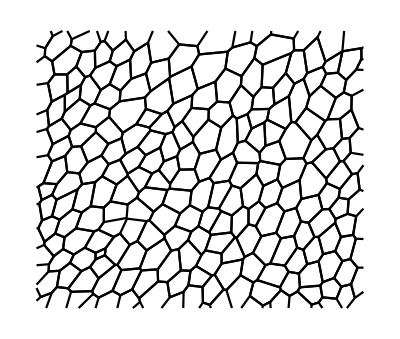

Tension coefficients computed: ☑

counts of zero coefficients Tx: 16

counts of zero coefficients Ty: 9

Tx coefficients stats: <|3→378,2→16,4→1|>

Ty coefficients stats: <|3→385,2→9,4→1|>

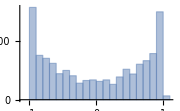
Tension coefficients distribution: -Graphics-

Pressure coefficients computed: ☑

Pressure coefficients zero: 15

Px coefficients stats: <|3→389,2→5,4→1|>

Py coefficients stats: <|3→384,4→1,2→10|>

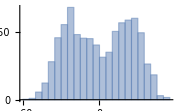
pressure coefficients distribution: -Graphics-

Maximum Likelihood Estimate

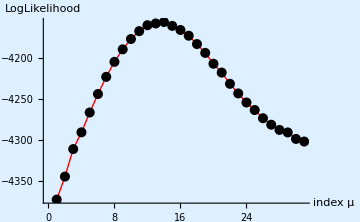

optimum value of μ is 0.630957 @ index 14

Tension map:

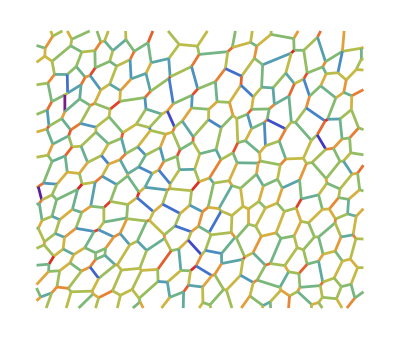

Pressure map:

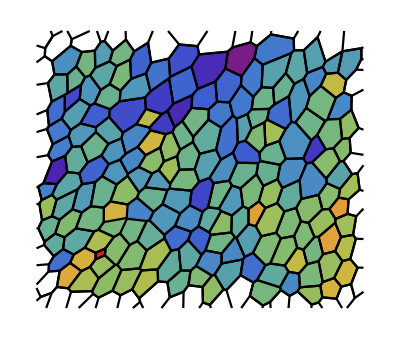

{36.2234,Null}

```mathematica
SetOptions[ForceInference,"mergers"-> True];
Quiet[AbsoluteTiming@ForceInference["D:\\LocalData\\hashmial\\scripts\\Force-Inference-master\\Force-Inference-master\\for ReadMe\\image.tif"]]
```

local stress map:

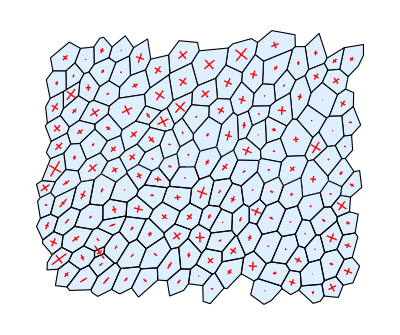

```mathematica
Print["local stress map:"];
localStressTensorMap[$cells,$edgeAssoc,$pvals,$tensionAssoc,2000]
```

global stress tensor map:

-Graphics-

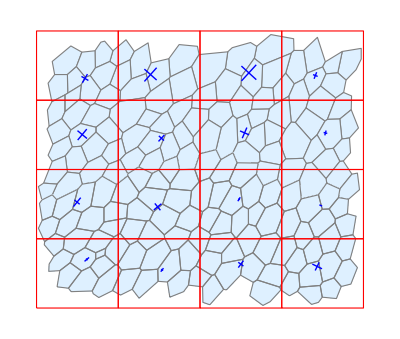

```mathematica
Print["global stress tensor map:"];
image=Import["D:\\LocalData\\hashmial\\scripts\\Force-Inference-master\\Force-Inference-master\\for ReadMe\\image.tif"];
globalStressTensorMap[image,{4,4},$cells,$edgeAssoc,$pvals,$tensionAssoc,5000]
```

### Example 2

kernels launched: {1,2,3,4,5,6}

-Graphics-

border exists, segmenting with watershed components

-Graphics-

Image segmented: ☑

vertices found and associated: ☑

-Graphics-

edges are merged

edges found and associated: ☑

-Graphics-

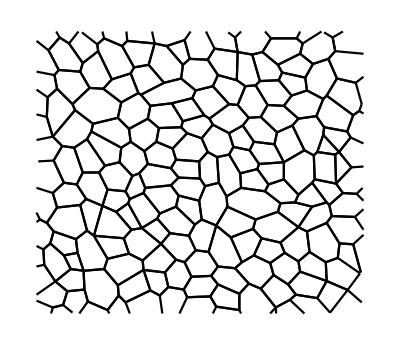

Tension coefficients computed: ☑

counts of zero coefficients Tx: 4

counts of zero coefficients Ty: 4

Tx coefficients stats: <|3→244,4→17,2→3,1→1|>

Ty coefficients stats: <|3→242,2→4,4→18,1→1|>

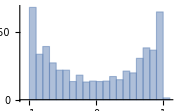
Tension coefficients distribution: -Graphics-

Pressure coefficients computed: ☑

Pressure coefficients zero: 13

Px coefficients stats: <|3→243,4→17,2→5|>

Py coefficients stats: <|3→240,4→18,2→7|>

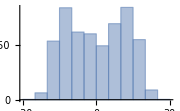
pressure coefficients distribution: -Graphics-

Maximum Likelihood Estimate

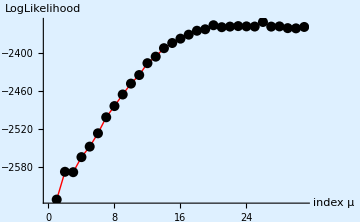

optimum value of μ is 10. @ index 26

Tension map:

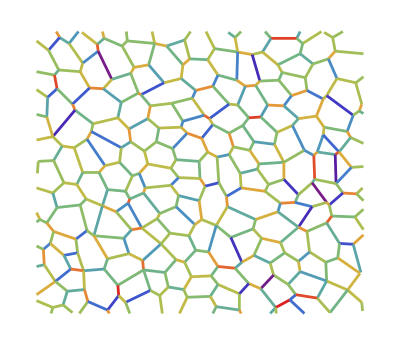

Pressure map:

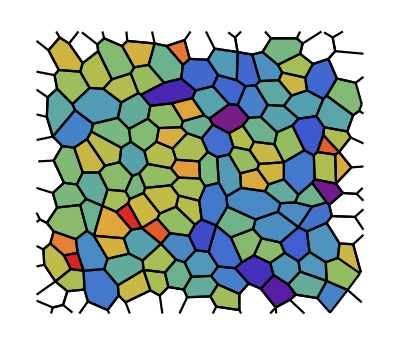

{7.18728,Null}

```mathematica
SetOptions[ForceInference,"mergers"-> True];
Quiet[AbsoluteTiming@ForceInference["D:\\LocalData\\hashmial\\Data from Irene\\IY embryoimages\\Cropping and Correction\\11\\proper\\quad1mod_iter - 2.tif"]]
```

local stress map:

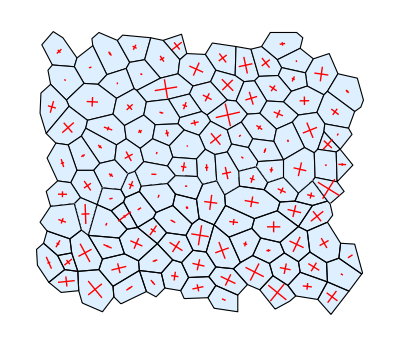

```mathematica
Print["local stress map:"];
localStressTensorMap[$cells,$edgeAssoc,$pvals,$tensionAssoc,500]
```

global stress tensor map:

-Graphics-

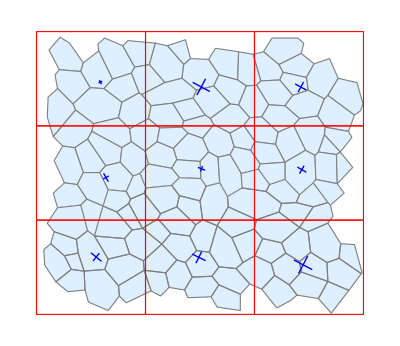

```mathematica
Print["global stress tensor map:"];
image=Import["D:\\LocalData\\hashmial\\Data from Irene\\IY embryoimages\\Cropping and Correction\\11\\proper\\quad1mod_iter - 2.tif"];
globalStressTensorMap[image,{3,3},$cells,$edgeAssoc,$pvals,$tensionAssoc,1000]
```